```mathematica
Series[1/√((x+1)^2+1-2(x+1) Cos[2θ]),{x,0,3}]//FullSimplify
```

1/(2 √(Sin[θ]^2))-x/(4 √(Sin[θ]^2))+((1-3 Cos[2 θ]) x^2)/(32 (Sin[θ]^2)^(3/2))+((1+5 Cos[2 θ]) x^3)/(64 (Sin[θ]^2)^(3/2))+O[x]^4

```mathematica
Series[1/√(x^2+1-2x Cos[2θ]),{x,1,3}]//FullSimplify
```

1/(2 √(Sin[θ]^2))-(x-1)/(4 √(Sin[θ]^2))+((1-3 Cos[2 θ]) (x-1)^2)/(32 (Sin[θ]^2)^(3/2))+((1+5 Cos[2 θ]) (x-1)^3)/(64 (Sin[θ]^2)^(3/2))+O[x-1]^4

```mathematica
Series[(Cos[2θ]-(x+1))/√((x+1)^2+1-2(x+1) Cos[2θ]),{x,0,3}]//FullSimplify
```

-√(Sin[θ]^2)-(Cos[θ]^2 x)/(2 √(Sin[θ]^2))+(3 Cos[θ]^2 x^2)/(8 √(Sin[θ]^2))+(Cos[θ]^2 (-3+5 Cos[2 θ]) x^3)/(32 (Sin[θ]^2)^(3/2))+O[x]^4

```mathematica
Series[(cos2theta-(x+1))/√((x+1)^2+1-2(x+1) Cos[2θ]),{x,0,3}]//FullSimplify
```

(-1+cos2theta)/(2 √(Sin[θ]^2))-((1+cos2theta) x)/(4 √(Sin[θ]^2))+((3+cos2theta-(1+3 cos2theta) Cos[2 θ]) x^2)/(32 (Sin[θ]^2)^(3/2))+((-3+cos2theta+(1+5 cos2theta) Cos[2 θ]) x^3)/(64 (Sin[θ]^2)^(3/2))+O[x]^4

```mathematica
sol=Solve[{Sin[2θ]/√((Δm1+1)^2+1-2(Δm1+1)Cos[2θ])==2sinx cosx,cosx^2-sinx^2==(Cos[2θ]-Δm1)/√((Δm1+1)^2+1-2(Δm1+1)Cos[2θ])},{sinx,cosx}]//FullSimplify
```

{{sinx→(√((Δm1-Cos[2 θ]-√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))/(√2),cosx→Sin[2 θ]/(√2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]-√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))},{sinx→-(√((Δm1-Cos[2 θ]-√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))/(√2),cosx→-(√2 Cos[θ] Sin[θ])/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]-√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))},{sinx→-(√((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))/(√2),cosx→-(√2 Cos[θ] Sin[θ])/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))},{sinx→(√((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))/(√2),cosx→Sin[2 θ]/(√2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))}}

```mathematica
Series[sinx/.sol[[2]],{Δm1,0,1}]//FullSimplify;
Series[sinx/.sol[[4]],{Δm1,0,1}]//FullSimplify
Series[cosx/.sol[[4]],{Δm1,0,1}]//FullSimplify
Series[sinx/.sol[[3]],{Δm1,0,1}]//FullSimplify
Series[cosx/.sol[[3]],{Δm1,0,1}]//FullSimplify
```

1/2 √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2)))+1/8 √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2))) (-1+2 √(Csc[θ]^2) √(Sin[θ]^2)) Δm1+O[Δm1]^2

Sin[2 θ]/(2 √(Sin[θ]^2) √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2))))+(((2 √(Csc[θ]^2)+1/(√(Sin[θ]^2))) Sin[2 θ]+1/2 (-√(Csc[θ]^2)-2/(√(Sin[θ]^2))) Sin[4 θ]) Δm1)/(8 √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2))) (-1+Cos[2 θ] √(Csc[θ]^2) √(Sin[θ]^2)))+O[Δm1]^2

-1/2 √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2)))+1/8 √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2))) (1-2 √(Csc[θ]^2) √(Sin[θ]^2)) Δm1+O[Δm1]^2

-(Cos[θ] Sin[θ])/(√(Sin[θ]^2) √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2))))+(3 Csc[θ]^2 Sin[2 θ] Δm1)/(8 (2 √(Csc[θ]^2)-1/(√(Sin[θ]^2))) √(√(Csc[θ]^2)-Cos[2 θ]/(√(Sin[θ]^2))))+O[Δm1]^2

```mathematica
Series[Sin[2θ]/(Cos[2θ]-hatDeltam1-1),{hatDeltam1,0,2}]
```

Sin[2 θ]/(-1+Cos[2 θ])+(Sin[2 θ] hatDeltam1)/(-1+Cos[2 θ])^2+(Sin[2 θ] hatDeltam1^2)/(-1+Cos[2 θ])^3+O[hatDeltam1]^3

```mathematica
theta1=ArcTan[Sin[2 θ]/(-1+Cos[2 θ])+(Sin[2 θ] hatDeltam1)/(-1+Cos[2 θ])^2]/2(*ArcTan[Sin[2θ]/(Cos[2θ]-hatDeltam1-1)]/2 *)
```

1/2 ArcTan[(hatDeltam1 Sin[2 θ])/(-1+Cos[2 θ])^2+Sin[2 θ]/(-1+Cos[2 θ])]

```mathematica
Series[Sin[theta1],{hatDeltam1,0,2}]//FullSimplify
```

-Sin[1/2 ArcTan[Cot[θ]]]+1/4 Cos[1/2 ArcTan[Cot[θ]]] Cot[θ] hatDeltam1+1/32 Cot[θ]^2 (4 Cos[1/2 ArcTan[Cot[θ]]] Cot[θ]+Sin[1/2 ArcTan[Cot[θ]]]) hatDeltam1^2+O[hatDeltam1]^3

```mathematica
Sin[4t]-4Sin[t]Cos[t]Cos[2t]//FullSimplify
```

0

```mathematica
transM={{cosx,sinx},{-sinx,cosx}}/.sol[[4]]/.sol[[4]];
%//MatrixForm
```

(Sin[2 θ]/(√2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))) | (√((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))/(√2)
-(√((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))/(√2) | Sin[2 θ]/(√2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))))

```mathematica
transMD=D[transM,Δm1]//Simplify;
%//MatrixForm
```

(-(((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) Sin[2 θ])/(2 √2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) ((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))^(3/2))+((-1-Δm1+Cos[2 θ]) Sin[2 θ])/(√2 (2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))) | (((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(2 √2 √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))
-(((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(2 √2 √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))) | -(((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) Sin[2 θ])/(2 √2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) ((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))^(3/2))+((-1-Δm1+Cos[2 θ]) Sin[2 θ])/(√2 (2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))))

```mathematica
v=-I derivativeDeltaHat Transpose[transM].transMD//Simplify;
%//MatrixForm
```

(-ⅈ derivativeDeltaHat (1/4 ((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+(Sin[2 θ] (-(((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) Sin[2 θ])/(2 √2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) ((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))^(3/2))+((-1-Δm1+Cos[2 θ]) Sin[2 θ])/(√2 (2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))))/(√2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))) | -(ⅈ derivativeDeltaHat (1+Δm1^2+Δm1 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])+Cos[2 θ] (-2 Δm1-√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))) Sin[2 θ])/(2 (1+Δm1^2-2 Δm1 Cos[2 θ]) (2 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+2 Δm1 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+Δm1^2 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+Δm1 √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])+Cos[2 θ] (-2 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))-2 Δm1 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))-√(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))))
(ⅈ derivativeDeltaHat (1+Δm1^2+Δm1 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])+Cos[2 θ] (-2 Δm1-√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))) Sin[2 θ])/(2 (1+Δm1^2-2 Δm1 Cos[2 θ]) (2 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+2 Δm1 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+Δm1^2 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+Δm1 √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])+Cos[2 θ] (-2 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))-2 Δm1 √((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))-√(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))) | -ⅈ derivativeDeltaHat (1/4 ((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ]))+(Sin[2 θ] (-(((√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])))/(1+Δm1^2-2 Δm1 Cos[2 θ])+(-1-Δm1+Cos[2 θ])/((2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2))) (Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) √(2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])) Sin[2 θ])/(2 √2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) ((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])))^(3/2))+((-1-Δm1+Cos[2 θ]) Sin[2 θ])/(√2 (2+2 Δm1+Δm1^2-2 (1+Δm1) Cos[2 θ])^(3/2) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))))/(√2 √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]) √((Δm1-Cos[2 θ]+√((1+Δm1^2-2 Δm1 Cos[2 θ])/(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ])) √(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))/(√(2+Δm1 (2+Δm1)-2 (1+Δm1) Cos[2 θ]))))))

```mathematica
Series[v,{Δm1,0,1}]//Simplify;
%//MatrixForm
```

((ⅈ derivativeDeltaHat (1+2 Cos[2 θ]) (-4 Cos[2 θ]+(3+Cos[4 θ]) √(Csc[θ]^2) √(Sin[θ]^2)))/(16 √(Sin[θ]^2) (-1+Cos[2 θ] √(Csc[θ]^2) √(Sin[θ]^2))^2)-1/512 ⅈ derivativeDeltaHat (8 (Csc[θ]^2)^(3/2)-32 Cos[4 θ] (Csc[θ]^2)^(3/2)-16 Csc[θ]^6 √(Sin[θ]^2)+19 Cos[2 θ] Csc[θ]^6 √(Sin[θ]^2)+Cos[6 θ] (8 (Csc[θ]^2)^(3/2)-3 Csc[θ]^6 √(Sin[θ]^2))+(2 Cot[θ]^2 √(Sin[θ]^2) (-868+312 Cos[6 θ]-124 Cos[8 θ]+8 Cos[10 θ]-2 Cos[12 θ]-798 √(Csc[θ]^2) √(Sin[θ]^2)+411 Cos[6 θ] √(Csc[θ]^2) √(Sin[θ]^2)-74 Cos[8 θ] √(Csc[θ]^2) √(Sin[θ]^2)+23 Cos[10 θ] √(Csc[θ]^2) √(Sin[θ]^2)-2 Cos[4 θ] (463+396 √(Csc[θ]^2) √(Sin[θ]^2))+2 Cos[2 θ] (672+743 √(Csc[θ]^2) √(Sin[θ]^2))))/((-1+Cos[2 θ] √(Csc[θ]^2) √(Sin[θ]^2))^5)) Δm1+O[Δm1]^2 | -1/2 ⅈ derivativeDeltaHat Cos[θ] √(Csc[θ]^2) Sin[θ]+(ⅈ derivativeDeltaHat (-1+2 Cos[2 θ]) Csc[θ]^2 ((-6-2 Cos[4 θ]+Cos[6 θ]) √(Csc[θ]^2)+Cos[2 θ] (7 √(Csc[θ]^2)+16 √(Sin[θ]^2))) Sin[2 θ] Δm1)/(64 (-1+Cos[2 θ] √(Csc[θ]^2) √(Sin[θ]^2))^2)+O[Δm1]^2
1/2 ⅈ derivativeDeltaHat Cos[θ] √(Csc[θ]^2) Sin[θ]-(ⅈ derivativeDeltaHat (-1+2 Cos[2 θ]) Csc[θ]^2 ((-6-2 Cos[4 θ]+Cos[6 θ]) √(Csc[θ]^2)+Cos[2 θ] (7 √(Csc[θ]^2)+16 √(Sin[θ]^2))) Sin[2 θ] Δm1)/(64 (-1+Cos[2 θ] √(Csc[θ]^2) √(Sin[θ]^2))^2)+O[Δm1]^2 | (ⅈ derivativeDeltaHat (1+2 Cos[2 θ]) (-4 Cos[2 θ]+(3+Cos[4 θ]) √(Csc[θ]^2) √(Sin[θ]^2)))/(16 √(Sin[θ]^2) (-1+Cos[2 θ] √(Csc[θ]^2) √(Sin[θ]^2))^2)-1/512 ⅈ derivativeDeltaHat (8 (Csc[θ]^2)^(3/2)-32 Cos[4 θ] (Csc[θ]^2)^(3/2)-16 Csc[θ]^6 √(Sin[θ]^2)+19 Cos[2 θ] Csc[θ]^6 √(Sin[θ]^2)+Cos[6 θ] (8 (Csc[θ]^2)^(3/2)-3 Csc[θ]^6 √(Sin[θ]^2))+(2 Cot[θ]^2 √(Sin[θ]^2) (-868+312 Cos[6 θ]-124 Cos[8 θ]+8 Cos[10 θ]-2 Cos[12 θ]-798 √(Csc[θ]^2) √(Sin[θ]^2)+411 Cos[6 θ] √(Csc[θ]^2) √(Sin[θ]^2)-74 Cos[8 θ] √(Csc[θ]^2) √(Sin[θ]^2)+23 Cos[10 θ] √(Csc[θ]^2) √(Sin[θ]^2)-2 Cos[4 θ] (463+396 √(Csc[θ]^2) √(Sin[θ]^2))+2 Cos[2 θ] (672+743 √(Csc[θ]^2) √(Sin[θ]^2))))/((-1+Cos[2 θ] √(Csc[θ]^2) √(Sin[θ]^2))^5)) Δm1+O[Δm1]^2)

## OOOOO

Using first order Δ̂(x)=Δ̂(x_r)+Δ̂'(x_r)(x-x_r)

```mathematica
sol2=Solve[{Sin[2θ]/√((alph+1)^2+1-2(alph+1)Cos[2θ])==2sinx cosx,cosx^2-sinx^2==(Cos[2θ]-(1+alph))/√((alph+1)^2+1-2(alph+1)Cos[2θ])},{sinx,cosx}]//FullSimplify
```

{{sinx→(√((1+alph-Cos[2 θ]-√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2),cosx→-1/(√2)(1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ])) √(-(-1-alph+Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))) Csc[2 θ]},{sinx→-(√(-(-1-alph+Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2),cosx→1/(√2)(1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ])) √(-(-1-alph+Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))) Csc[2 θ]},{sinx→-(√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2),cosx→1/(√2)(1+alph-Cos[2 θ]-√(2+alph (2+alph)-2 (1+alph) Cos[2 θ])) √((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))) Csc[2 θ]},{sinx→(√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2),cosx→1/(√2)√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))) (-1-alph+Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ])) Csc[2 θ]}}

```mathematica
Series[1/√((1+lam (x-xr))^2+1-2(1+lam(x-xr) )Cos[2θ])]
```

1/(√(1+(1+lam (x-xr))^2-2 (1+lam (x-xr)) Cos[2 θ]))

```mathematica
{{Cos[thetax],Sin[thetax]},{-Sin[thetax],Cos[thetax]}}.{-1,1}.{}
```

```mathematica
Series[(√((1+alph-Cos[2 θ]-√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2),{alph,0,2}]
```

1/2 √(-2+√2 √(1-Cos[2 θ]))+((1+Cos[2 θ]) alph)/(4 √2 √(-2+√2 √(1-Cos[2 θ])) √(1-Cos[2 θ]))+(√(-2+√2 √(1-Cos[2 θ])) (1+Cos[2 θ]) (-7 √2+12 √(1-Cos[2 θ])+5 √2 Cos[2 θ]) alph^2)/(32 √2 (-√2+2 √(1-Cos[2 θ])+√2 Cos[2 θ])^2)+O[alph]^3

```mathematica
Series[(√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2),{alph,0,2}]
```

1/2 √(2+√2 √(1-Cos[2 θ]))+((1+Cos[2 θ]) alph)/(4 √2 √(2+√2 √(1-Cos[2 θ])) √(1-Cos[2 θ]))+(√(2+√2 √(1-Cos[2 θ])) (1+Cos[2 θ]) (-7 √2-12 √(1-Cos[2 θ])+5 √2 Cos[2 θ]) alph^2)/(32 √2 (-√2-2 √(1-Cos[2 θ])+√2 Cos[2 θ])^2)+O[alph]^3

```mathematica
Series[1/(√2)√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))) (-1-alph+Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ])) Csc[2 θ],{alph,0,1}]
```

1/2 √(2+√2 √(1-Cos[2 θ])) (-1+√2 √(1-Cos[2 θ])+Cos[2 θ]) Csc[2 θ]-(((1+√2 √(1-Cos[2 θ])+√2 √(1-Cos[2 θ]) Cos[2 θ]-Cos[2 θ]^2) Csc[2 θ]) alph)/(4 (√2 √(2+√2 √(1-Cos[2 θ])) √(1-Cos[2 θ])))+O[alph]^2

```mathematica
Series[sinx/.sol2[[4]],{alph,0,1}]
Series[cosx/.sol2[[4]],{alph,0,1}]
```

1/2 √(2+√2 √(1-Cos[2 θ]))+((1+Cos[2 θ]) alph)/(4 √2 √(2+√2 √(1-Cos[2 θ])) √(1-Cos[2 θ]))+O[alph]^2

1/2 √(2+√2 √(1-Cos[2 θ])) (-1+√2 √(1-Cos[2 θ])+Cos[2 θ]) Csc[2 θ]-(((1+√2 √(1-Cos[2 θ])+√2 √(1-Cos[2 θ]) Cos[2 θ]-Cos[2 θ]^2) Csc[2 θ]) alph)/(4 (√2 √(2+√2 √(1-Cos[2 θ])) √(1-Cos[2 θ])))+O[alph]^2

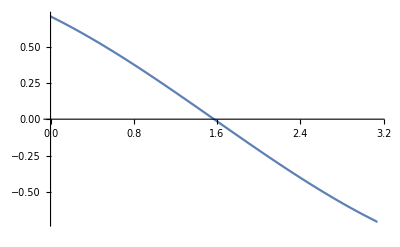

```mathematica
Plot[1/2 √(2+√2 √(1-Cos[2 θ])) (-1+√2 √(1-Cos[2 θ])+Cos[2 θ]) Csc[2 θ],{θ,0,Pi}]
```

The transformation matrix U_m is

```mathematica
um[alph_]={{cosx,sinx},{-sinx,cosx}}/.sol2[[4]]//FullSimplify
```

{{1/(√2)√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))) (-1-alph+Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ])) Csc[2 θ],(√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2)},{-(√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))))/(√2),1/(√2)√((1+alph-Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))/(√(2+alph (2+alph)-2 (1+alph) Cos[2 θ]))) (-1-alph+Cos[2 θ]+√(2+alph (2+alph)-2 (1+alph) Cos[2 θ])) Csc[2 θ]}}

```mathematica
Transpose[um[alph]].(D[um[alph],alph])//FullSimplify
%//MatrixForm
```

{{0,Sin[2 θ]/(2 (2+alph (2+alph)-2 (1+alph) Cos[2 θ]))},{-Sin[2 θ]/(2 (2+alph (2+alph)-2 (1+alph) Cos[2 θ])),0}}

(0 | Sin[2 θ]/(2 (2+alph (2+alph)-2 (1+alph) Cos[2 θ]))
-Sin[2 θ]/(2 (2+alph (2+alph)-2 (1+alph) Cos[2 θ])) | 0)

```mathematica
Series[Sin[2 θ]/(2 (2+alph (2+alph)-2 (1+alph) Cos[2 θ])),{alph,0,1}]
```

-Sin[2 θ]/(4 (-1+Cos[2 θ]))+(Sin[2 θ] alph)/(4 (-1+Cos[2 θ]))+O[alph]^2

### Whatever

```mathematica
D[√(x^2+1-2x Cos[2θ]),x]//FullSimplify
```

(x-Cos[2 θ])/(√(1+x^2-2 x Cos[2 θ]))